# Investigating Ecological Energy and Colony Population Dynamics with Agent-Based Modeling Systems

Yash Juneja

Om Kalyani

Shreraj Sainani

## Abstract

In this work, we present a custom bioenergetics-informed ecological Agent-Based Modeling (ABM) toolbox for colonies of artificial organisms in the Wolfram Language. We investigated  energy and population dynamics with connections to real-world biology using this toolbox. Unlike previous Agent-Based Modeling projects done in the Wolfram Language, our interactive toolbox provides the user with the ability to change and visualize the effects of the parameters used by the artificial colonies such as resolution of simulation time-discretization, sensing and interaction abilities of organisms, metabolic rates, lifespans, exploration/foraging behaviors, reproductive frequencies, and bioenergetics like digestion and reproduction energies. Our tests show that ecological models produced by the toolbox mimic population dynamics on a macro-level as seen in real-world ecology through experimentation on metabolic rates, primary production rates, caloric densities and reproductive frequencies with a logistic analysis of population growth and collection of other demographic data.

## Introduction

We developed an agent-based modeling toolbox to study how simple bioenergetic rules shape population-level dynamics. In the model, individual agents move through an environment bounded by a square, sense food, interact with other agents, consume energy, reproduce, age, and die. Each agent follows relatively simple rules, and the population as a whole can show certain emergent behaviors that will be discussed in this study, such as logistic growth, carrying capacity, variation in reproduction timing, and differences in mortality. The toolbox’s simulation logic incorporates movement, organisms dynamically sensing their environment and adjusting foraging and mating decisions, energy consumption, reproduction, and aging, as well as a visualization that maps each timestep to show how agents undergo all of these behaviors, which are informed through bioenergetics. Bioenergetics is the study of how organisms acquire, transform, store, and expend energy, and how those energy flows determine biological outcomes like growth, reproduction, movement, and survival  [RN1]. With this ‘toolbox,’ we test how environmental and biological parameters affect population outcomes. Specifically, we vary factors such as food availability, metabolism, reproduction energy cost, and reproduction age, then record their effects on population size, carrying capacity, growth rate, first reproduction age, and lifespan. Since our model has limited space that introduces competition between agents (if two agents attempt to eat the same food it is determined randomly which eats it) and a constrained amount of food that is spawned (simulating primary production in an ecosystem), the environment has a limited potential for growth, and the populations of colonies were accordingly found to naturally trend towards logistic growth. Logistic growth is governed by the following differential equation, which embeds the constrained nature of the population growth into its structure with the (1-P/K) factor [NG1]:

dP/dt= rP(1-P/K)		(1)

Separating and integrating this differential equation gives the form that we use among other curves to fit to our population data among other data for analysis

P(t)= K/(1 + Ae^(-r t))		(2)

Where K represents carrying capacity, r represents intrinsic growth rate, and A represents the relationship between the initial population and carrying capacity. These variables allow us to compare how different parameter values affect population-level behavior as a whole.

	Overall, through these experiments, we show how simple rules can influence a population’s dynamics and characteristics, and how our Agent-Based Modeling toolbox can be used as a flexible foundation for studying further ecological systems and emergent population-level and agent-level behaviors not only because it exhibits such behavior like logistic growth, but also because of its flexibility from the infinite possibilities its large number of customizable parameters provides.

## High-Level Model Development

We designed our Agent-Based model from the ground up to be customizable for the user, making it easy to run experiments and test hypotheses. The simulation is complete with visuals and animations, showing what’s going on behind the raw data. All behavior, except for random movement when needed, is deterministic and always based on the starting parameters. It is important to note that agents do not “feel” or are not provided “rewards” by the simulation. Rather, natural selection drives some agents to do better than others, causing other agents to die out, showing how certain parameters support life better or worse.
	Agents are organisms with age and energy, must consume resources to survive, move, reproduce, and optionally invest energy in offspring. When deciding on what action an agent takes every time step, we took inspiration from a British Ecological Society paper outlining the general order of importance:

“If there is sufficient energy intake, an animal allocates the energy obtained in the order: maintenance, growth, reproduction, energy storage, until its energy stores reach an optimal level. If there is a shortfall, the priorities for maintenance and growth/reproduction remain the same until reserves fall to a critical threshold below which all are allocated to maintenance.” - [RS1]

In our model, agents unavoidably lose energy every time step through “metabolism.” When deciding to take an action, in the agentActions function, we first look at if the agent meets all the criteria to reproduce. This includes having enough energy, having another non-related agent in the sensing radius, not being on a reproduction cooldown, and having existed for long enough. Agents need a minimum amount of energy before looking to reproduce because growth/sustenance is of a higher priority than reproduction [RS1]. If there is no suitable mate, the agent then looks for food in proximity. If it is close enough, it eats it. If not, the agent moves towards the food. And finally, if the agent doesn’t see anything in its radius, it picks a random exploration direction and walks. The agent has a random chance to change directions every time step when exploring, so it is able to more effectively explore a single direction before looking elsewhere. If an agent tries to leave the bounds, its position is clipped to the bounds, and if it is half a step away from the bounds, the direction it is moving in changes. The environment supplies food containing energy every timestep to simulate primary production (usually plants producing organic matter from sunlight) in the ecosystem. Because of this, the organisms we simulate are primary consumers.

## Model Parameters

These are model parameters stored as an association that set the rules for a simulation, and a user may freely tweak them to model certain environmental scenarios or use these as independent variables to run empirical experiments. Most functions of the model take in this parameters association to understand how they should work and to what extent their functions should affect model/agent state. Comments following each parameter outlines its purpose. Parameters, and thus the model, is defined in nondimensionalized arbitrary units: arbitrary distance units denoted (D), arbitrary time units denoted (T), and arbitrary energy units denoted (E) throughout.

```mathematica
parameters = <|
   "proximityRadius" -> 0.5, (*How close two things (agent/food, agent/agent) need to be to interact (eat, reproduce, etc.)*)
   "sensingDistance" -> 4, (*How far agents can sense items*)
   "metabolism" -> 0.05,
   "dt" -> 0.1, (*timestep*)
   
   (* Food/environment *)
   "foodEnergy" -> 5.0,
   "foodSpawnCooldown" -> 1,
   "nFoodSpawn" -> 5,
   "nStartingFood" -> 4,
   
   (* Initial population and movement *)
   "nStartingAgents" -> 4,
   "squareBounds" -> {0, 20},
   "startingEnergy" -> 10,
   "stepLength" -> 0.4,
   "dirChangeProb" -> 0.025,
   "lifespan" -> 30,
   "maxEnergy" -> 10,
   
   (* Visualization *)
   "imageSize" -> 500,
   "agentSize" -> 0.01,
   "foodSize" -> 0.0075,
   
   (* Reproduction *)
   "reproductionRadius" -> 1.0,
   "minReproductionEnergy" -> 5.0,
   "minReproductionAge" -> 4.0,
   "reproductionEnergyCost" -> 2.0,
   "reproductionCooldown" -> 2,
   
   (* Variables for numerical stability *)
   "epsilon" -> 0.001,
   "rnd" -> N@10^-3
|>;
```

## Core Model

### Data Structures

Before the rest of the toolbox was built, the core aspects of the model like agents that moved and consumed food were built first. The food in a model at any time is represented by a list of positions of pieces of food. For the data structure of the model as a whole, see Model Initialization.

createAgent[]is used to initialize agent associations, and their states can be accessed through keys. Each agent attribute is commented with a description of its nature

```mathematica
createAgent[pos_, energy_, age_, id_, currentDirection_, parents_:{-1, -1}, reproductionCooldown_] := <|
    "pos" -> pos, (*The current position of an agent in the environment, length 2 array*)
    "energy" -> energy, (*The current energy of an agent*)
    "age" -> age, (*The current age of an agent*)
	"id" -> id, (*A unique identifer given to each agent created throughout the history of the simulation instance*)
	"currentDirection" -> currentDirection, (*The current direction the agent is exploring in or seeking food/mates in; value from [0, 2pi)*)
	"parents" -> parents, (*The ids of the agent's parents in a length 2 array. If the agent is one of the primordial starting agents, {-1, -1} is given to this value.
	used to determine familial relations for the purpose of incest prevention--a parent will naturally not reproduce with their child throughout almost all species*)
    "reproductionCooldown" -> reproductionCooldown
|>
```

### Core Functions

These functions are the basic operations needed for core model functionality.

For any interactions to occur, an object must be within another’s proximityRadius.  This goes for an agent and a piece of food, an agent and another agent for reproduction.

```mathematica
checkWithinRadius[p1_, p2_, r_] := EuclideanDistance[p1, p2] <= r;
```

EuclidianDistance[] is used in the checkWithinRadius[] function to verify the interaction condition of proximityRadius throughout simulation.

A function called findNearestSensableFoodInfo[] is used to find the nearest sensable (within sensingDistance) food to an agent so agents can seek and eat food. It returns this nearest sensable food’s distance, index in the food list, and position.

```mathematica
findNearestSensableFoodInfo[agent_, foodPositions_List, params_] := Module[
    {agentPos, foodPosAndI, foodsWithinRadiusPosAndI, dists},
    agentPos = agent["pos"];
    foodPosAndI = Table[{foodPositions[[i]], i}, {i, Length[foodPositions]}];
    foodsWithinRadiusPosAndI = Select[foodPosAndI, checkWithinRadius[agentPos, #[[1]], params["sensingDistance"]]&];
    If[
        Length[foodsWithinRadiusPosAndI] == 0,
        {-1, -1, -1}, (*no food*)
        dists = {EuclideanDistance[agentPos, #[[1]]], #[[2]], #[[1]]}& /@ foodsWithinRadiusPosAndI;
        First@MinimalBy[dists, First]
    ]
]
```

The function first compiles the food positions and indexes, and then isolates the ones that are within sensing distance of the agent. If no pieces of food make it into that isolation, then there are none within sensing distance and {-1, -1, -1} is returned. Else, the closest food’s {distance, index in the food list, position in the environment} is returned.

spawnFoods[]takes in a food list and adds new foods with the amount corresponding to the nFoodSpawn parameter. Rounding is used to prevent excess precision which increases the memory needed to save a simulation to a file (17.988838327 takes up more space then 17.989 in a .csv file).

```mathematica
spawnFoods[foods_, params_] := Join[foods, Round[RandomReal[params["squareBounds"], {params["nFoodSpawn"], 2}], params["rnd"]]]
```

To spawn food at the appropriate time, spawnFoodCheck[] updates the model’s food list with a spawnFoods[]operation when appropriate according to the foodSpawnCooldown parameter.

```mathematica
spawnFoodCheck[model_, params_] := Module[
    {model2 = model},
	model2["foods"] = If[
        Mod[model["time"], params["foodSpawnCooldown"]] < 10^(-1),
        spawnFoods[model["foods"], params],
        model["foods"]
    ];
	model2
]
```

< 10^(-1) is used instead of  == 0 to not have to worry about integer vs. float mismatch issues (see Future Direction).

randomizeAndKill[] is a simulation management function that kills agents if they’ve reached any death conditions and randomizes their order within the agent list. This function is called at every timestep to ensure no agents are consistently prioritized as our food consumption and reproduction helper functions choose the first agent in the list.

```mathematica
randomizeAndKill[model_, params_] := Module[
    {agents = model["agents"], model2=model},	
	agents = RandomSample[agents];
	model2["agents"] = Select[agents, (#["age"] < params["lifespan"] && #["energy"] > 0)&];
	model2
]
```

metabolizeAgents[]applies the metabolism operation to all agents for a timestep.

```mathematica
metabolizeAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# - params["metabolism"])&, agents, {All, "energy"}];
	model2["agents"] = agents;
	model2
]
```

ageAgents[]ages agents by one timestep dt during a timestep.

```mathematica
ageAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# + params["dt"])&, agents, {All, "age"}];
	model2["agents"] = agents;
	model2
]
```

explorationOrIntentionalWalk[] is the function that makes an agent walk in the current direction it’s moving in. This current direction depends on the sensory input an agent receives from its environment, and this heading is determined in the agentActions[]function in Agent Rules and Behavior.

```mathematica
explorationOrIntentionalWalk[agent_, params_] := Module[ (*direction is set in agentActions[], depending on exploration or intentional*)
	{agent2 = agent, currentDir = agent["currentDirection"], newPos, min, max},
	{min, max} = params["squareBounds"];
	newPos = agent2["pos"] + {params["stepLength"] * currentDir[[1]], params["stepLength"] * currentDir[[2]]};
	agent2["pos"] = Clip[newPos, {min, max}];
	agent2
]
```

agentEat[]is used to update agents’ energy when they eat a piece of food according to the foodEnergy parameter. The specific food that is being eaten is removed concurrently when this function is called from the model’s food list in the agentActions[]function in Agent Rules and Behavior.

```mathematica
agentEat[agent_, params_] := Module[
    {agent2 = agent, newE},
	newE = agent2["energy"] + params["foodEnergy"];
	agent2["energy"] = If[newE > params["maxEnergy"], params["maxEnergy"], newE];
	agent2
]
```

Through the If[]statement in the function, agentEat[] ensures that the energy does not exceed the maxEnergy

## Reproduction

Introducing reproduction is crucial to simulate real animal behaviors. When two agents meet, they produce an offspring that inherits a position between them and a fresh slice of energy. Our functionality has four main parts working together: a way to give every agent an identity, rules for deciding who is allowed to mate with whom, and the reproduction step itself.

Every agent has a unique integer id, assigned when the agent is created. Every agent also has the ids of both their parents. The founding agents, the first agents in the simulation, have no parents and are simply marked with {-1, -1}. These are all part of the agent association (see createAgent[]in Data Structures).

The nextAgentId is created in initializeModel[](see Model Initialization) to one more than the founding population, so the first agent created is given the next unused id: 

"nextAgentID" -> nStartingAgents + 1

### Helper Functions

areRelated[ai, aj] returns True if two agents share a close family tie, and is used to prevent incestuous pairings. It checks three conditions joined by an Or[] statement: whether aj’s id appears in ai’s parent list (aj is a parent of ai), whether ai is a parent of aj, or whether the two agents have the identical set of parents (making them siblings). The sibling check sorts both parent lists before comparing so that parent order does not matter, and it explicitly excludes the founding agents, whose parents are {-1, -1}, so that the original population is not treated as one large sibling group.

```mathematica
areRelated[ai_, aj_] := Or[
    MemberQ[ai["parents"], aj["id"]],   
    MemberQ[aj["parents"], ai["id"]], 
    (ai["parents"] =!= {-1, -1} && Sort[ai["parents"]] === Sort[aj["parents"]])  (* siblings: same parent pair *)
]
```

A reproduction cooldown is needed because, without one, any qualifying pair would reproduce on every single timestep they remained close and energetic, producing unrealistic runaway population growth. This is also necessary to reflect biology as most organisms cannot reproduce many times in one period and instead require some recovery or storage of energy before reproducing again. The cooldown imposes a refractory period: after reproducing, an agent’s reproductionCooldown is set to a positive value and it cannot mate again until that value returns to 0. decrementReproductionCooldowns[] is what counts it down - each timestep it reduces every agent’s reproductionCooldown by the model’s timestep dt, using Max[# - dt, 0] so the value never drops below zero, at which point the agent becomes eligible to reproduce again.

```mathematica
decrementReproductionCooldowns[model_, params_] := Module[
    {agents = model["agents"], model2 = model},
	agents = MapAt[Max[# - params["dt"], 0]&, agents, {All, "reproductionCooldown"}];
	model2["agents"] = agents;
	model2
]
```

findClosestAgentI[] returns the index of the closest agent to an agent in question in the model’s agents list. It is necessary for the Main Reproduction Function below.

```mathematica
findClosestAgentI[agentI_Integer, agents_List] := Module[
    {pos, dists},
    If[Length[agents] < 2, Return[-1]];
    pos = agents[[agentI]]["pos"];
    dists = Table[
        If[i == agentI, Infinity, EuclideanDistance[pos, agents[[i]]["pos"]]],
        {i, Length[agents]}
    ];
    First@Ordering[dists, 1]
]
```

The Ordering[]function is the main sorting workhorse of findClosestAgentI[]. The If statement avoids conflating oneself for the nearest agent through use of Infinity.

### Main Reproduction Function

reproduceAgents[] carries out the actual reproduction step for a timestep. It iterates over every agent and finds its closest candidate partner, then re-checks the full mating predicate inline (the same distance, energy, age, cooldown, and relatedness conditions). When a pair qualifies and neither partner has already reproduced this timestep, both parents pay their parametric reproductionEnergyCost and have their cooldown reset, and a new agent is created at the midpoint between the parents with half of the model’s preset startingEnergy parameter for an agent, age 0, the next unused id, a random heading (see Agent Rules and Behavior), and both parents’ ids recorded. The new id counter advances, both partners are flagged as having reproduced so each mates at most once per step, and at the end the newborns are appended to the population and nextAgentID is saved back into the model.

```mathematica
reproduceAgents[model_, params_] := Module[
    {
        agents = model["agents"], model2 = model, newAgents = {},
        reproduced, nextID, j, ai, aj, dist, midPos, newAgent, newDir
    },

  nextID = model["nextAgentID"];
  reproduced = ConstantArray[False, Length[agents]];

  Do[
    If[reproduced[[i]], Continue[]];
    j = findClosestAgentI[i, agents];
    If[j == -1 || reproduced[[j]], Continue[]];

    ai = agents[[i]];
    aj = agents[[j]];
    dist = EuclideanDistance[ai["pos"], aj["pos"]];

    If[dist <= params["reproductionRadius"] &&
       ai["energy"] >= params["minReproductionEnergy"] &&
       aj["energy"] >= params["minReproductionEnergy"] &&
       ai["age"] >= params["minReproductionAge"] &&
       aj["age"] >= params["minReproductionAge"] &&
        ai["reproductionCooldown"] <= 0 &&
        aj["reproductionCooldown"] <= 0 &&
       !areRelated[ai, aj],

      (* both parents pay energy cost *)
      agents[[i]] = <|ai,
      "energy" -> ai["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;
      agents[[j]] = <|aj,
      "energy" -> aj["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;

      midPos = (ai["pos"] + aj["pos"]) / 2;
      newDir = {Cos[#], Sin[#]} &[RandomReal[{0, 2 Pi}]];
      newAgent = createAgent[midPos, params["startingEnergy"]/2, 0.0, nextID, newDir, {ai["id"], aj["id"]}, params["reproductionCooldown"]];
      AppendTo[newAgents, newAgent];
      nextID++;

      reproduced[[i]] = True;
      reproduced[[j]] = True;

    ];
  , {i, Length[agents]}];

  model2["agents"] = Join[agents, newAgents];
  model2["nextAgentID"] = nextID;
  model2
]
```

## Agent Rules and Behavior

### Helper Functions

An array of helper functions create the functionality for agents to navigate and interact with their surroundings according to pre-established biological rules. Agent decision making is not probabilistic and instead follows the principles of bioenergetics (see Main Agent Decision Logic below).

The first such helper function is findClosestMateI[]. This function is identical to findClosestAgentI[]above in Reproduction except for the fact that areRelated[]is used to exclude parental or sibling relations. This is still done in the Main Reproduction Function when findClosestAgentI[] is used, making this a minor redundancy in the package.

```mathematica
findClosestMateI[agentI_Integer, agents_List] := Module[
    {pos, dists, agent},
    If[Length[agents] < 2, Return[-1]];
    pos = agents[[agentI]]["pos"];
    agent = agents[[agentI]];
    dists = Table[
        If[i == agentI || areRelated[agent, agents[[i]]], Infinity, EuclideanDistance[pos, agents[[i]]["pos"]]],
        {i, Length[agents]}
    ];
    First@Ordering[dists, 1]
]
```

The next such helper function, findNearestSensableMateInfo[]is similar in function and process to findNearestSensableFoodInfo[]in the Core Functions of the model. It employs findClosestMateI[]from above for the majority of its work and returns {-1, -1, -1} in the case that no mate nearby is sensable similar to findNearestSensableFoodInfo[]. Otherwise, just like that function, it returns the closest sensable mate’s {distance, index in the agents list, and position} of course.

```mathematica
findNearestSensableMateInfo[agentI_Integer, agents_List, params_] := Module[
	{agent, nearAgentI, nearAgent, nearAgentPos, nearAgentDist},
	agent = agents[[agentI]];
	nearAgentI = findClosestMateI[agentI, agents];
	nearAgent = agents[[nearAgentI]];
	nearAgentPos = nearAgent["pos"];
	nearAgentDist = EuclideanDistance[agent["pos"], nearAgentPos];
	If[nearAgentDist < params["sensingDistance"], {nearAgentDist, nearAgentI, nearAgentPos}, {-1, -1, -1}]
]
```

The following two functions agentSetFoodDir[] and agentSetMateDir[]are identical in form and different only in name for clarity. These functions orient the agent’s currentDirection direction vector (list of length 2) towards an agent or piece of food that it hopes to travel to, supplied with its index in its respective list (agents list or food list). This direction vector is of course calculated through vector subtraction and normalization. This is necessary for agents to be able to intentionally travel to their goal after sensing their goal in their environment. A smoothing parameter in the model epsilon is used to avoid numerical divergences in case agents are very close.

```mathematica
agentSetFoodDir[agent_, foodPos_, params_] := Module[
	{agent2 = agent, dirV},
	dirV = foodPos - agent["pos"];
	agent2["currentDirection"] = (1/(Norm[dirV]+params["epsilon"])) * dirV;
	agent2["currentDirection"] = Round[agent2["currentDirection"], params["rnd"]];
	agent2
]

agentSetMateDir[agent_, matePos_, params_] := Module[
	{agent2 = agent, dirV},
	dirV = matePos - agent["pos"];
	agent2["currentDirection"] = (1/(Norm[dirV] + params["epsilon"])) * dirV;
	agent2["currentDirection"] = Round[agent2["currentDirection"], params["rnd"]];
	agent2
]
```

Finally, agentSetExploreDir[] is the mechanism for agents’ foraging behavior. When agents are not intentionally traveling towards a mate or piece of food, they are exploring for those things. This is in a random direction, which has a probability of changing given by the model parameter dirChangeProb every timestep. An agent will definitely change its explore direction regardless of this probability if it has encountered a mate or piece of food according to the Main Agent Decision Logic below. By considering if agents are nearing the end the environment positionally, wall avoidance is implemented in the main Which[] statement. As per this statement, agents will head in their new exploration direction if they reach the random change of dirChangeProb or if they are on a collision course with a wall of the environment. If neither of those things happen they happily continue on their way.

```mathematica
agentSetExploreDir[agent_, params_] := Module[
	{agent2 = agent, ax, ay, sqmin, sqmax, proxRad, randomTheta},
	{ax, ay} = agent["pos"];
	{sqmin, sqmax} = params["squareBounds"];
	proxRad = params["stepLength"]/2;
	agent2["currentDirection"] = 
	Which[
		RandomReal[] < params["dirChangeProb"] || (ax < sqmin + proxRad || ax > sqmax - proxRad || ay < sqmin + proxRad || ay > sqmax - proxRad),
		randomTheta = RandomReal[{0, 2 Pi}]; Round[{Cos[randomTheta], Sin[randomTheta]}, params["rnd"]], 
		
		True,
		agent2["currentDirection"]
	];
	agent2
]
```

### Main Agent Decision Logic

The agentActions[] function is where the bio-energetic decisions and behaviors of agents is represented in our simulation. It governs how each agent chooses to use the opportunities provided to them in a timestep, depending on the conditions of their environment. According to bioenergetics, once an agent is maintained and surviving, it allocates its energy towards reproduction, only until after then does it focus on accumulating excess energy [RS1]. The agent’s main logic follows this.

```mathematica
agentActions[model_, params_] :=  Module[
    {model2 = model, agents = model["agents"], agentsSnapshot, foods = model["foods"], agent, 
    nearFoodDist, nearFoodI, nearFoodPos, nearMateDist, nearMateI, nearMatePos},
    agentsSnapshot = agents;
	agents = Table[
		agent = agents[[i]];
		{nearFoodDist, nearFoodI, nearFoodPos} = findNearestSensableFoodInfo[agent, foods, params];
		{nearMateDist, nearMateI, nearMatePos} = findNearestSensableMateInfo[i, agentsSnapshot, params];
		Which[
			And[
				agent["age"] > params["minReproductionAge"],
				agent["reproductionCooldown"] == 0,
				agent["energy"] > params["minReproductionEnergy"],
				nearMateI>=1
			],
			agent = agentSetMateDir[agent, nearMatePos, params]; agent = explorationOrIntentionalWalk[agent, params]; agent,
			
            nearFoodI>=1 && nearFoodDist < params["proximityRadius"], 
			foods = Delete[foods, nearFoodI]; agentEat[agent, params], 
			
			nearFoodI>=1,
			agent = agentSetFoodDir[agent, nearFoodPos, params]; agent = explorationOrIntentionalWalk[agent, params]; agent, 
			
			True,
			agent = agentSetExploreDir[agent, params]; agent = explorationOrIntentionalWalk[agent, params]; agent
        ],
	    {i, Length@agents}
    ];
	model2["foods"] = foods;
	model2["agents"] = agents;
	model2
]
```

The function iterates through all agents, updating them once they have undertaken their actions. First, an agent senses its environment through calls to findNearestSensableFoodInfo[] and findNearestMateInfo[]. Once it has this information, it follows this bioenergetically-informed logic:

Does an agent meet all the criteria for reproduction with a nearby agent? i.e. has it satisfied its needs of maintenance and survival?

These criteria are being old enough to reproduce (above the minReproductionAge parameter), having completed the reproductionCooldown, having the minReproductionEnergy, and having an agent even near you in the first place. This last one is determined from the result of findNearestMateInfo[].

If yes, then setMateDir[]is used to orient the agent towards a mate and explorationOrIntentionalWalk[]allows it to take one step in the direction of that agent (simply deciding which direction to go does not take up a timestep). Reproduction automatically happens outside of agentActions[] according to the rules set out in the Reproduction section if agents are near enough, almost like a bonus action.

If no, then continue

Is the agent near a piece of food and is it close enough to eat it?

If yes, then eat it, gain some energy, the food is gone. Delete[]is used to delete the food from the food list based on the sensory information provided by findNearestSensableFoodInfo[] (the index along with other information about specific piece of food the agent is eating)

If no, then continue

Does the agent even see (sense) any food?

If yes, then travel towards it. agentSetFoodDir orients the agent towards it, and explorationOrIntentionalWalk[] allows the agent to take one step in that direction (simply deciding which direction to go does not take up a timestep).

Are none of the above true? i.e. does the agent not see any food and does it not meet any of the criteria for reproduction?

The agent will then explore (forage). agentSetExploreDir[] provides the agent with a new random exploration direction if it reaches the random probability for direction change, otherwise it will have it continue in its current exploration direction. explorationOrIntentionalWalk[] allows the agent to take one step in that exploration direction.

## Model Initialization

The initializeModel[] function returns an initialized model initialized according to the model parameters. The data structure for the model is an association that contains all the important information about the state of the model. The model has an agents list which is a list of all the agent associations in the current state of the model, the food list which is that for the food, the current bounds of the model, the time at which the model is currently at, and the nextAgentID identification stored, which operates as described in the Reproduction section.

```mathematica
initializeModel[params_] :=

  Module[{agents, foods, nStartingAgents, nStartingFood, startingEnergy, min, max, randomDir},  

    nStartingAgents = params["nStartingAgents"]; (*parameter for number of agents*)
    nStartingFood = params["nStartingFood"]; (*parameter for number of food items*)
    startingEnergy = params["startingEnergy"];
    {min, max} = params["squareBounds"];

    agents =
    Table[
      randomDir = RandomReal[{0, 2 Pi}];
      createAgent[Round[RandomReal[{min, max}, 2], params["rnd"]], startingEnergy, 0.0, i, Round[{Cos[randomDir], Sin[randomDir]}, params["rnd"]], params["reproductionCooldown"]], {i, nStartingAgents}
    ];

    foods = Round[RandomReal[{min, max}, {nStartingFood, 2}], params["rnd"]];
	
    <| 
      "agents" -> agents, (*list of agent associations*)
      "foods" -> foods, (*list of food coordinates*)
      "bounds" -> {min, max},
      "time" -> 0,
      "nextAgentID" -> nStartingAgents + 1
    |>
 ]
```

The association returned is the model with the association data structure as described above.

## Model Propagation

The propagateModelStep[] function propagates the model by one timestep, doing the operations that occur during a timestep sequentially: spawning food if it’s the appropriate time,  removing agents that are dead and randomizing their order of priority for competition between similar mates and pieces of food, doing the main agent action decision logic, decrementing reproduction cooldowns, performing the reproduction bonus action, subtracting energy for metabolism, aging agents, and finally advancing the stored time in the simulation.

```mathematica
propagateModelStep[params_, model_] := Module[{model2=model},
  model2 = spawnFoodCheck[model2, params];
  model2 = randomizeAndKill[model2, params]; (*randomization*)
  model2 = agentActions[model2, params];
  model2 = decrementReproductionCooldowns[model2, params];
  model2 = reproduceAgents[model2, params]; 
  model2 = metabolizeAgents[model2, params];
  model2 = ageAgents[model2, params];
  model2["time"] = model2["time"] + params["dt"];
  model2
 ];
```

genSimulationStates[] is used to generate the entire simulation, which becomes a list of model states, with each index in the list being being a model object representing the state of the simulation after an amount of time steps that is that index.

```mathematica
genSimulationStates[params_, model_, timesteps_] := Module[{model2 = model}, Join[{model},Table[model2 = propagateModelStep[params, model2];model2,{s, timesteps}]]]
```

genSimulationStates[] performs its operations on a supplied model object. As such, initializeModel[]must be called to initialize such a model if one does not already exist (first starting a simulation). genSimulation[] is a function that just does this as well for ease of use.

```mathematica
genSimulation[params_, tsteps_] := genSimulationStates[params, initializeModel[params], tsteps]
```

These are then rendered frame by frame, for visualization purposes, or this simulation data is exported for data analysis. For experiments and exporting simulations, we use the .wdx format because it is significantly more compressed than .csv files and created two custom import functions for our simulation data based off of Wolfram’s native Import[] and Export[] functions. Those are not discussed here but can be seen in the project Github repository [make sure to link that somewhere].

## Producing the Simulation Object

genSimulation[] is ran with the desired amount of timesteps as a parameter to produce the simulation object, stored in a variable. For example, here it is stored in the variable Simulation1 and ran for 1000 timesteps, a relatively small amount in comparison to the potential of the toolbox (please give it a maximum of 1 minute to run). Evidently, the parameters used here were those defined at the top of this essay in Model Parameters.

```mathematica
Simulation1000 = genSimulation[parameters, 1000];
```

## Analysis

With our toolbox, there are built in functions for analysis of simulations and the potential for many more to be created by the user. The first and foremost tool is the plotPopulationStats[] function which plots the population and food count of a simulation over its history.

```mathematica
plotPopulationStats[simulation_List] := Module[
  {times, agentCounts, foodCounts},
  times = #["time"] & /@ simulation;
  agentCounts = Length[#["agents"]] & /@ simulation;
  foodCounts = Length[#["foods"]] & /@ simulation;

  ListLinePlot[
    {agentCounts, foodCounts},
    DataRange  -> {First[times], Last[times]},
    PlotLegends -> {"Agents", "Food"},
    PlotStyle  -> {Blue, Green},
    AxesLabel  -> {"Time", "Count"},
    PlotLabel  -> "Population Over Time",
    GridLines  -> Automatic,
    ImageSize  -> 500
  ]
]
```

Calling this function on the Simulation1 object we generated earlier will allow us to see the outcome of the simulation we generated with the parameters that we used. We can observe the characteristic logistic growth behavior in the population with fluctuations around the carrying capacity

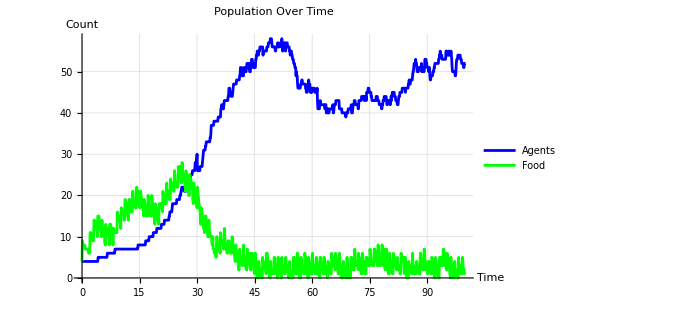

```mathematica
plotPopulationStats[Simulation1000]
```

The toolbox includes functions to analyze this carrying capacity and logistic growth behavior. The showLogsitic[] function below shows this population curve fitted to the equation P(t) = K/(1 + Ae^-rt), where K is the carrying capacity, r is the intrinsic growth rate, and A is an amplitude constant that contains information about the initial population among other things. showLogistic[] employs Wolfram’s NonlinearModelFit[] for its least-squares regression.

```mathematica
showLogistic[simulation_] := Module[{agentCounts, times, series, fit},
	agentCounts = Length@#[[1]]& /@ simulation;
	times = #[[4]]& /@ simulation;
	series = Transpose[{times, agentCounts}];
	
	fit = NonlinearModelFit[
	    series,
	    K/(1 + A Exp[-r t]),
	    {{K, 35}, {A, 10}, {r, 1}},
	    t];
	   
	Show[
		ListLinePlot[series],
		Plot[fit[x], {x, times[[1]], times[[-1]]}]
	]
]
```

Calling the function on our simulation, we can see the curve fitted...

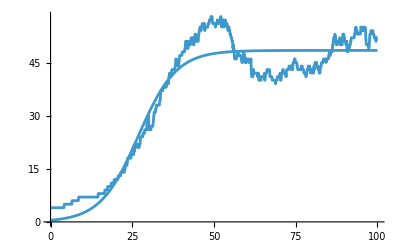

```mathematica
showLogistic[Simulation1000]
```

The logisticStats[]function allows for extraction of K, A, and r. It is as below, and calling it on our simulation gives us the carrying capacity K and intrinsic growth rate r of the artificial colony in the environment modeled under the parameters of this essay undergoing 1000 timesteps of forward simulation.

```mathematica
logisticStats[simulation_] := Module[{agentCounts, times, series, fit},
	agentCounts = Length@#[[1]]& /@ simulation;
	times = #[[4]]& /@ simulation;
	series = Transpose[{times, agentCounts}];
	
	fit = NonlinearModelFit[
	    series,
	    K/(1 + A Exp[-r t]),
	    {{K, 35}, {A, 10}, {r, 1}},
	    t];
	
	Association@fit["BestFitParameters"]
]
```

```mathematica
logisticStats[Simulation1000]
```

<|K→48.4115,A→101.008,r→0.172052|>

Another type of analysis our toolbox allows one to do is look at population demographic distributions like the agents by their age at first reproduction, which is very useful to see how quickly agents are able to find mates once they reach reproductive maturity (set by the parameter minReproductionAge), which is essential for species survival. This can be influenced negatively by sparsity of agents or competition when the population is near carrying capacity. Below is an example of such analysis on a simulation run with the exact same parameters as here over 2000 timesteps.

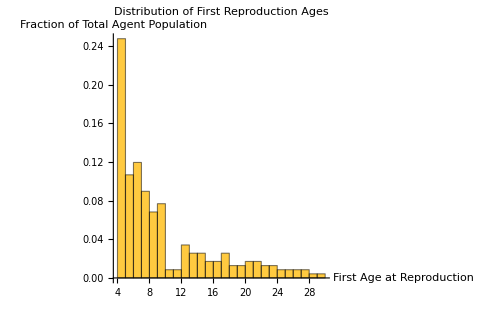
Mean Age at First Reproduction: 9.70
Median Age at First Reproduction: 7.40
How Many Agents Reproduced: 234
Number of Timesteps: 2000
-Graphics-

The distribution of first reproduction ages shows that most agents reproduce almost immediately after reaching the minimum reproduction age, which, in this experiment, was set to 4. Moreover, this suggests that the environment is rich in resources and thus conducive to the population’s growth, as agents can have sufficient energy and food to reproduce immediately and find mates. Additionally, the median first reproduction age of 7.40 furthers this pattern, indicating that at least half of the agents reproduce early in their lifespans. Also, the distribution is right-skewed, which explains the disparity between the mean and median age at first reproduction (9.70 and 7.40, respectively). Most agents reproduce before 10 T of age, which is 6 T after they reach reproductive maturity. There are however some, that do not until later ages, and this likely occurs in high-competition scenarios near carrying capacity. A quarter of the agents reproduced as soon as possible before reaching an age of 5 T.

## Visualization

Two scaling functions are used to convert between D units and pixels for the image based on the parameters of the model

```mathematica
lUnitsToPixels[lUnits_, params_] := lUnits * (params["imageSize"]/(params["squareBounds"][[2]] - params["squareBounds"][[1]]))
lPixelsToUnits[lPixels_, params_]:= lPixels * ((params["squareBounds"][[2]] - params["squareBounds"][[1]])/params["imageSize"])
```

For our visualization, we created a function called displayGrid which styles the text, energy bars, etc. and formats the agents with the function drawAgentGraphic. Initially, we combined all these aspects of our code into displayGrid itself by using the Module function inside of Table, but we found that using a separate function, such as drawAgentGraphic, to handle other formatting allows us to significantly increase efficiency. First, we gather the following information

```mathematica
agents, foods, min, max, span, nAgents,
    hudPad, agentR, foodR, barW, barH, barGap,
    showEnergyBars, legendX, legendY, infoX, infoY,
    agentGraphics, foodGraphics, legend, infoText
```

To simulate how agents interact with one another in an environment, we created a square visualization window bounded by the parameter squareBounds to render agents, food/resources, energy levels, ages, and other characteristics for each timestep. The function first extracts all agent information from the main association.

```mathematica
agents = model["agents"];
  foods = model["foods"];
  {min, max} = params["squareBounds"];
```

Additionally, an important variable is span, which we use to scale the visualization with the size of the modeled world, so the display remains consistent even when the environment changes.

```mathematica
span = max - min;
```

Since the bounds of the environment can change, we scaled the graphics to the bound of the world. Specifically, if the environment is small, agents and food appear larger, whereas if the environment is large, the agents appear smaller.

```mathematica
agentR = params["agentSize"]*span;
  foodR  = params["foodSize"]*span;

  barW = 0.10 span;
  barH = 0.015 span;
  barGap = 0.040 span;

  hudPad = 0.001 span;
```

To keep the visualization clean and prevent the grid from looking ‘crowded’ as the population increases, we used the current population size to control how much detail to display. As a result, energy bars are only shown when there are less than 6 agents

```mathematica
showEnergyBars = nAgents < 6;
```

The agents’ properties, such as age and energy level, are represented by color gradients. Specifically, age is shown by a green (young agent) to red (old agent) gradient. It is important to note that the agents’ ages are relative to their total lifespan. This allows us to display the age visually, without crowding the grid with other legends.

```mathematica
ageColor[age_] := Blend[
    {Green, Yellow, Orange, Red},
    Clip[age/(0.3 params["lifespan"]), {0, 1}]
  ];
```

We also switch the text color between black and white, depending on each agent’s age, to keep the age readable against different gradient colors.

```mathematica
ageTextColor[age_] := If[age < 0.6 params["lifespan"], Black, White];
```

The energy of each agent is represented by a red-to-green bar, in which red represents low energy, while green represents a high energy. These energy levels are relative to the max energy defined in the associations.

```mathematica
energyColor[frac_] := Blend[
    {Red, Yellow, Green},
    Clip[frac, {0, 1}]
  ];
```

Initially, we found it difficult to avoid overlap between text/agent information when agents are close together in the grid. So, to fix this, we wrote a helper rule to check agent positions and test multiple possible locations for the energy bar. Now, the function takes into account the positions above, below, left, and right, clips them to stay inside the grid, and, by using a scoring method, finds what position maximizes distance from nearby agents. Overall, this makes the visualization more readable.

```mathematica
otherAgentPositions[pos_] := DeleteCases[Lookup[agents, "pos"], pos];
  chooseBarCenter[pos_, others_] := Module[{candidates, scores}, candidates = {pos + {0, barGap}, pos + {0, -barGap}, pos + {barGap, 0}, pos + {-barGap, 0}};
    
    candidates = {
      {Clip[candidates[[1, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[1, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[2, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[2, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[3, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[3, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[4, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[4, 2]], {min + barH/2, max - barH/2}]}};
       
    scores = If[Length[others] == 0,ConstantArray[1, Length[candidates]],Min[Norm[# - #2] & @@@ Tuples[{{#}, others}]] & /@ candidates];
    candidates[[First @ Ordering[scores, -1]]]];
```

Within drawAgentGraphic, we extract each agent’s information and create local variables for the agent’s position, age, energy, energy fraction, display colors, and energy-bar placement.

```mathematica
pos = agent["pos"];
age = agent["age"];
e = agent["energy"];
```

Then, we convert each agent’s energy into a fraction between 0 to 1, which controls both the length and the color of the energy bar. The variable percent creates the number that is displayed in the energy bar.

```mathematica
frac = Clip[e/params["maxEnergy"], {0, 1}];
percent = Round[100 frac];
```

Moreover, the following lines determine the agent’s circle color based on age and choose a legible text color for the age label.

```mathematica
fillColor = ageColor[age];
txtColor = ageTextColor[age];
```

One of the most difficult yet important aspects for our project was choosing the correct energy bar placement. We created a function that tests possible positions around the agent and chooses the location that is farthest from other agents while staying inside the simulation bounds.

```mathematica
barCenter = chooseBarCenter[pos, otherAgentPositions[pos]];
barLeft = barCenter[[1]] - barW/2;
barBottom = barCenter[[2]] - barH/2;

 {EdgeForm[Directive[White, Thickness[0.0015]]],fillColor,Disk[pos, agentR],Text[Style[ToString[Round[age]],Max[7, Round[0.018 params["imageSize"]]],txtColor,Bold],pos],
 If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{barLeft, barBottom},{barLeft + barW, barBottom + barH}],energyColor[frac],
 Rectangle[{barLeft, barBottom},{barLeft + barW frac, barBottom + barH}], Text[Style[ToString[percent],Max[6, Round[0.014 params["imageSize"]]],Magenta],barCenter]},Nothing]}],{agent, agents}];
```

Additionally, we used small white disks to represent food in our simulations.

```mathematica
foodGraphics = Table[{White, Disk[f, foodR]},{f, foods}];
```

For clarity, we added a legend to the top left of the grid to explain labels for the agents, energy bars, and food. It also shows the current time, remaining food count, and number of agents in the model. To ensure that the legend stays consistent for varying bounds, we anchored it relative to squareBounds. Additionally,

```mathematica
legendX = min + hudPad;
  legendY = max - hudPad;

  infoX = max - hudPad;
  infoY = max - hudPad;

  legend = {Text[Style["Legend", 11, White, Bold],{legendX, legendY},{-1, 1}],
  EdgeForm[Directive[White, Thickness[0.0015]]],ageColor[0.2 params["lifespan"]],Disk[{legendX + 0.020 span, legendY - 0.050 span}, params["foodSize"]*span*1.3],Text[Style["Agent", 9, White],{legendX + 0.042 span, legendY - 0.050 span},{-1, 0}],

    If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.070 span, legendY - 0.077 span}],energyColor[0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.0525 span, legendY - 0.077 span}],
        Text[Style["Energy", 9, White],{legendX + 0.085 span, legendY - 0.0835 span},{-1, 0}]},Nothing],White,Disk[{legendX + 0.020 span, legendY - 0.130 span}, params["foodSize"]*span],Text[Style["Food", 9, White],{legendX + 0.042 span, legendY - 0.130 span},{-1, 0}]};

  infoText = Text[Style[Column[{"Time: " <> ToString @ NumberForm[model["time"], {4, 2}],"Food Count: " <> ToString @ Length[foods],"Agents: " <> ToString @ nAgents},
        Alignment -> Right],11,White],{infoX, infoY},{1, 1}];
```

For the purposes of explaining our visualization process, important functions were broken up into separate code cells for display that cannot run. Please ensure the following closed code cell, which is just those in the above section combined properly, is executed along with the rest of the cells, to define and enable our toolbox’s visualization functionality.

```mathematica
ageColor[age_, params_] := 
  Blend[{Green, Yellow, Orange, Red},
    Clip[age/(0.3 params["lifespan"]), {0, 1}]
  ];

ageTextColor[age_, params_] := If[age < 0.6 params["lifespan"], Black, White];

energyColor[frac_] := Blend[{Red, Yellow, Green}, Clip[frac, {0, 1}]];

otherAgentPositions[pos_, agents_] := DeleteCases[Lookup[agents, "pos"], pos];

chooseBarCenter[pos_, others_, min_, max_, barW_, barH_, barGap_] := Module[{candidates, scores},

  candidates = {
    pos + {0, barGap},
    pos + {0, -barGap},
    pos + {barGap, 0},
    pos + {-barGap, 0}
  };

  candidates = ({Clip[#[[1]], {min + barW/2, max - barW/2}], 
                 Clip[#[[2]], {min + barH/2, max - barH/2}]} &) /@ candidates;

  scores = If[
    Length[others] == 0,
    ConstantArray[1, Length[candidates]],
    Min[Norm[# - #2] & @@@ Tuples[{{#}, others}]] & /@ candidates
  ];

  candidates[[First @ Ordering[scores, -1]]]
];
 
(* 
  - drawAgentGraphic creates the graphics for one individual agent (agent circle, age counter, and energy bar)
  - Helps reduce bloat b/c this method allows us to avoid using Module inside of Table
  - Can consider putting this method inside of basicMethods.wl
*)

drawAgentGraphic[agent_, agents_, params_, min_, max_, span_, agentR_, barW_, barH_, barGap_, showEnergyBars_] := Module[
  {
    pos, age, e, frac, percent,
    fillColor, txtColor,
    barCenter, barLeft, barBottom
  },

  (* get each agent's position, age, and energy from the agent association *)
  
  pos = agent["pos"];
  age = agent["age"];
  e = agent["energy"];

(* convert the agent's current energy into a fraction from 0 to 1 so that we can use it to find the energy bar length & color*)
  frac = Clip[e/params["maxEnergy"], {0, 1}];
  percent = Round[100 frac];

  fillColor = ageColor[age, params]; (*younger agents are greener, older agents are redder*)
  txtColor = ageTextColor[age, params];

  barCenter = chooseBarCenter[ (*this checks nearby agents and tries to place the bar in the least crowded area*)
    pos,
    otherAgentPositions[pos, agents],
    min, max, barW, barH, barGap
  ];

(*the bar's center becomes the lower left corner so the bar doesn't go over the boundaries*)
  barLeft = barCenter[[1]] - barW/2;
  barBottom = barCenter[[2]] - barH/2;

  {
    EdgeForm[Directive[White, Thickness[0.0015]]],
    fillColor,
    Disk[pos, agentR],
    Text[ (*display agent's rounded age*)
      Style[
        ToString[Round[age]],
        Max[7, Round[0.018 params["imageSize"]]],
        txtColor,
        Bold
      ],
      pos
    ],

    If[
      showEnergyBars, (*only showing energy bars when n<6*)
      {
      (*this code below defines specifics for the energy bar (color, numbers, size, etc.)*)
        EdgeForm[Directive[White, Thickness[0.0012]]],
        Darker[Gray, 0.75],
        Rectangle[{barLeft, barBottom}, {barLeft + barW, barBottom + barH}],
        energyColor[frac],
        Rectangle[{barLeft, barBottom}, {barLeft + barW frac, barBottom + barH}],
        Text[
          Style[
            ToString[percent],
            Max[6, Round[0.014 params["imageSize"]]],
            Magenta
          ],
          barCenter
        ]
      },
      Nothing (*if n>6, don't create the bars*)
    ]
  }
];

(* 
  - displayGrid renders the full simulation (food, agents, legend, time, agent count, etc.)
  - each agent is drawn by the drawAgentGraphic method
*)

displayGrid[model_, params_] := Module[ (*we should use conversion functions instead of span imo.*)
  {
    agents, foods, min, max, span, nAgents,
    hudPad, agentR, foodR, barW, barH, barGap,
    showEnergyBars, legendX, legendY, infoX, infoY,
    agentGraphics, foodGraphics, legend, infoText
  },

  agents = model["agents"];
  foods = model["foods"];
  {min, max} = params["squareBounds"];
  span = max - min;
  nAgents = Length[agents];

  agentR = lUnitsToPixels[params["agentSize"], params];
  foodR = lUnitsToPixels[params["foodSize"], params];

  barW = 0.10 span;
  barH = 0.015 span;
  barGap = 0.040 span;

  hudPad = 0.001 span;

  showEnergyBars = nAgents < 6;

  agentGraphics = drawAgentGraphic[#,agents,params,min,max,span,agentR,barW,barH,barGap,showEnergyBars] & /@ agents;

  foodGraphics = Table[{White,Disk[f, foodR]},{f, foods}];

  legendX = min + hudPad;
  legendY = max - hudPad;

  infoX = max - hudPad;
  infoY = max - hudPad;

  legend = {Text[Style["Legend", 11, White, Bold],{legendX, legendY},{-1, 1}],
  EdgeForm[Directive[White, Thickness[0.0015]]],ageColor[0.2 params["lifespan"], params],Disk[{legendX + 0.020 span, legendY - 0.050 span}, params["foodSize"]*span*1.3],Text[Style["Agent", 9, White],{legendX + 0.042 span, legendY - 0.050 span},{-1, 0}],

    If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.070 span, legendY - 0.077 span}],energyColor[0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.0525 span, legendY - 0.077 span}],
        Text[Style["Energy", 9, White],{legendX + 0.085 span, legendY - 0.0835 span},{-1, 0}]},Nothing],White,Disk[{legendX + 0.020 span, legendY - 0.130 span}, params["foodSize"]*span],Text[Style["Food", 9, White],{legendX + 0.042 span, legendY - 0.130 span},{-1, 0}]};

  infoText = Text[Style[Column[{"Time: " <> ToString @ NumberForm[model["time"], {4, 2}],"Food Count: " <> ToString @ Length[foods],"Agents: " <> ToString @ nAgents},
        Alignment -> Right],11,White],{infoX, infoY},{1, 1}];

  Graphics[{foodGraphics,agentGraphics,legend,infoText},
    Background -> Black,
    PlotRange -> {{min, max}, {min, max}},
    PlotRangePadding -> Scaled[0.01],
    ImagePadding -> 10,
    ImageSize -> params["imageSize"]
  ]
]
```

## Visualizing the Simulation

The renderSimulation[] generates a list of frames using the above displayGrid[]function to generate each frame. The renderSimulation[]takes in the simulation object, which itself is a list of model states, and applies that frame generation on each model state to produce the visualization.

```mathematica
renderSimulation[states_List, params_] := displayGrid[#, params] & /@ states
```

simVisualize[]is the main function that a user of the toolbox will use to view specific timesteps of the simulation. It uses Wolfram’s Manipulate to create a video-like interface for viewing the frames. Slowing down the playing of the manipulate object will allow the visualization to be viewed more clearly.

```mathematica
simVisualize[simulation_, params_, timestepStart_:1, timestepEnd_:Length@simulation_] := Module[{simulationGraphics},
	simulationGraphics = renderSimulation[simulation[[timestepStart;;timestepEnd]], params];
	Manipulate[simulationGraphics[[visualizeTimestep]], {visualizeTimestep, 1, Length@simulationGraphics, 1, Appearance->Labeled}, SaveDefinitions -> True]
]
```

Frame generation is one of the more computationally intensive processes in our toolbox, which is why it’s done separately from simulation generation. It’s still a necessary tool to see what’s going on with the artificial organisms and how they interact with each other and their environment. Let’s call simVisualize[]on our simulation stored in the Simulation1000 symbol. Specifically, let’s visualize timesteps 1 - 400 to see what the population looks like in its rapid growth stages, and timesteps 700 - 900 to see what it looks like when it’s reached its equilibrium carrying capacity.

Click the  button next to the frame slider to expand the options for viewing the simulation. Clicking the slower button  will make the simulation much clearer. After clicking the slow button a few times, click play  to see the simulation in action. This is the exact same simulation that analysis was done on before, since it’s all stored in the symbol Simulation1000.

```mathematica
simVisualize[Simulation1000, parameters, 1, 400]
```

```mathematica
simVisualize[Simulation1000, parameters, 700, 900]
```

If we wanted to see the entire simulation play out, the last two arguments would naturally be 1 and 1000. If one forgot the length of the simulation in timesteps, they could always do Length@Simulation1000 of course.

## Experimentation

To demonstrate the capabilities of our model and connect its results to those of real world biology, experiments are presented here. For clarity, just the results and not the code for these experiments is here. The latter may however be found in the project’s Github. Our importing and exporting system was used to save these simulations after they were run so we could perform analysis on them.

### Dependent Variable 1 - Carrying Capacity K

2000 timesteps were used for these simulations, and unless a variable is the independent variable in each of these experiments, the parameters of these simulation are as they are in this computational essay.

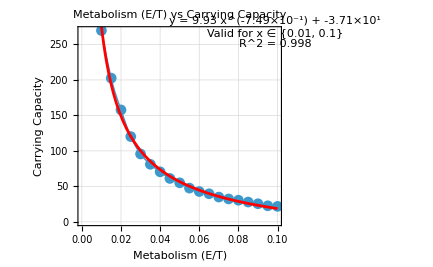
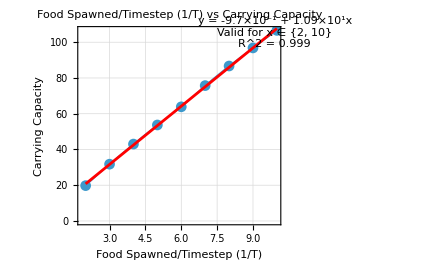

Metabolism (E/T) vs Carrying Capacity
This graph shows an inverse relationship between metabolism and carrying capacity. As the metabolic energy cost per timestep increases, the carrying capacity decreases drastically, which indicates that agents consume energy faster than they can replenish it through energy resources like food. This faster than linear decrease opposed to the food energy linear increases could possibly be explained by the fact that  having a higher metabolism causes compounding decreases in efficiency since metabolism occurs every timestep.The strong fit (R^2=0.998), which shows that metabolism is a limiting factor on long-term population stability. Moreover, at low metabolism values, agents can survive and reproduce more efficiently, whereas at high metabolism values, the environment can only sustain a smaller population before the low amounts of energy cause populations to decline.

Food Spawned per Timestep (1/T) vs Carrying Capacity
The second graph shows a positive linear relationship between food availability and carrying capacity. As the number of food particles spawned per timestep increases, the carrying capacity increases proportionally, which shows that the amount of food directly controls the maximum sustainable population size within the simulation. This is reinforced by the reliable fitness of the model (R^2=0.999), which suggests that under the current model assumptions, resource availability is one of the most important variables that controls population growth. Moreover, these results align well with ecological expectations, since an increase in resources naturally allows more organisms to maintain the necessary energy levels for survival and reproduction [BT1].

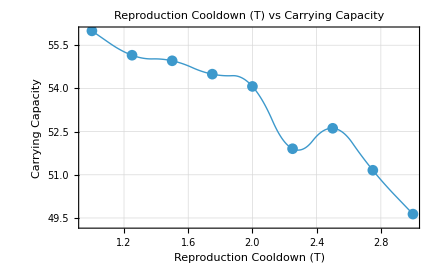
-Graphics--Graphics-

Food Energy (E) vs. Carrying Capacity
This graph shows a strong positive linear relationship between food energy and carrying capacity (R^2 = 0.988). Moreover, as the amount of energy supplied by each piece of food increases, populations can grow to large numbers and sustain themselves in the long-term because agents can replenish energy more efficiently each time they eat. Overall, this suggests that, regarding a population’s growth, the amount of food available may not necessarily play a larger role than the quality of the food. In fact, this shows that environments with more nutrient-dense pieces of food can support growing populations even when the amount of food remains constant or is lowered.

Reproduction Cooldown (T) vs. Carrying Capacity
This graph shows an overall negative relationship between reproduction cooldown and the carrying capacity of a population. As the cooldown increases, the carrying capacity decreases, likely because agents are limited to reproducing less frequently. However, the relationship is less smooth than in previous graphs; indeed, there are fluctuations present on the interval [2.0, 2.5], showing that reproduction cooldown has a more indirect effect on carrying capacity as opposed to other factors like food energy, reproduction cost, or metabolism. This is likely due to how reproduction timing aligns with the random movement of agents and food availability, which makes the impact of cooldown periods more sensitive to arbitrary events in the simulation.

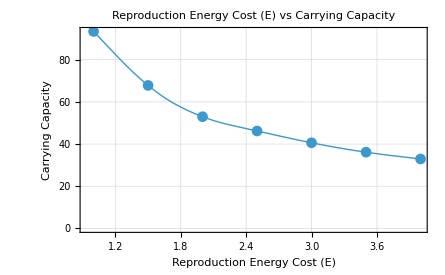

Reproduction Energy Cost (E) vs. Carrying Capacity
This graph shows an overall negative relationship between reproduction cooldown and the carrying capacity of a population. As the cooldown increases, the carrying capacity decreases, likely because agents are limited to reproducing less frequently. However, the relationship is less smooth than in previous graphs; indeed, there are fluctuations present on the interval [2.0, 2.5], showing that reproduction cooldown has a more indirect effect on carrying capacity as opposed to other factors like food energy, reproduction cost, or metabolism. This is likely due to how reproduction timing aligns with the random movement of agents and food availability, which makes the impact of cooldown periods more sensitive to arbitrary events in the simulation.

### Dependent Variable 2 - Intrinsic Growth Rate r

2000 timesteps were used for these simulations, and unless a variable is the independent variable in each of these experiments, the parameters of these simulation are as they are in this computational essay.

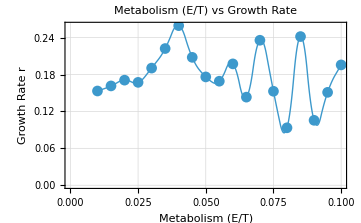
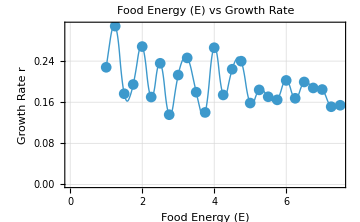

-Graphics--Graphics-

Unlike the carrying capacity curves, the growth rate curves all show several fluctuations rather than monotonic relationships. Moreover, the growth rate oscillates for the parameters like metabolism, food spawn rate, food energy, reproduction energy cost, and reproduction cooldown. This shows that in the simulation, the growth rate is extremely sensitive to events like random movement, locations of food spawning, or reproduction timing, likely more so then environmental parameters. Additionally, growth rate inherently measures the short-term changes in the population, making its curves seem much more unstable than carrying capacity, which measures the long-term equilibrium of a population. This further adds to the likelihood that small differences in how agents interact with the environments can impact the growth rate largely, noted that the environmental parameters that were used as independent variables in these experiments didn’t seem to have much of an effect. For example, the ability of agents to find each other early in the simulation history when the population is sparse significantly impacts the success of the future population and how quickly it grows.

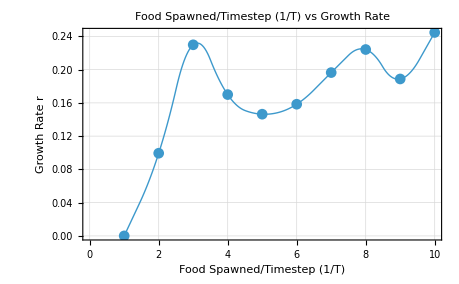

That being said, the Food Spawned/Timestep (1/T) vs. Growth Rate did seem to have a somewhat positive relationship, however indeterminate. The growth rate was 0 for 1 Food Spawned/Timestep because the food spawning rate was so low the population died off early. This relationship may be explained by the fact that more food allows agents to increase their energy reserves to the point where the reproductionCooldown becomes the only limiting factor on reproduction and not the amount of energy agents have. In other words, as more food is available, agents meet basic survival needs and can then focus on reproduction with maximum efficiency.

### Dependent Variable 3 - Life Expectancy

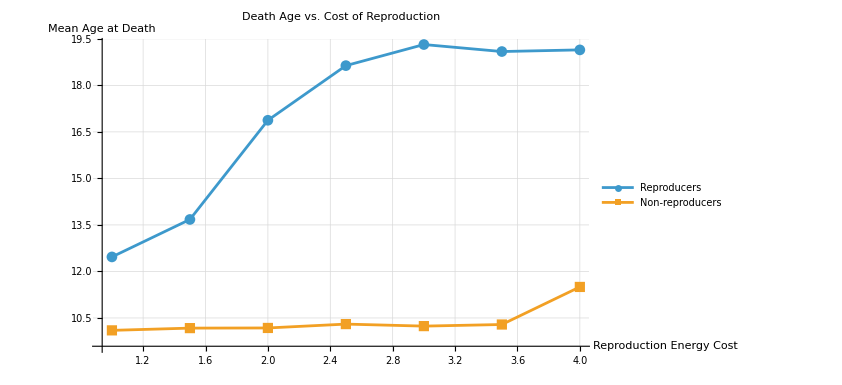

As the cost of reproduction energy increased, the average age at death for agents actually increased for reproducers. Agents were classified as reproducers if they had reproduced at least once in their instance of the simulation, and were otherwise classified as non-reproducers. In most ecosystems, as reproduction gets more expensive, we would expect to see average life spans to decrease, coming from the classic life-history trade-off prediction [GW1]. However, because our simulation doesn’t have predators, it’s a better model for isolated environments, like oceanic islands before human contact [IS1]. In these environments, organisms have low mortality factors and are able to live long lives with low reproduction rates due to a higher cost of reproduction. Interestingly, our ABM, starting with simple rules grounded in reality, happened to mimic real ecosystems for these variables too.

## Conclusion

Our model and its results show that changes in even a few simple biological rules can impact a population on a large scale. Effectively, by creating an ABM toolbox, we not only created an Agent-Based Modeling package for the Wolfram Community to use and extend, but we also demonstrated how populations respond to their surrounding environments, move, metabolize energy, reproduce, age, and die. Moreover, although each agent acts individually, our results corroborate with real-world biology, showing the artificial colonies in our simulation mimic real populations as they depict logistic growth, carrying capacity, variation in reproduction timing, and differences in mortality. Furthermore, we emphasize that even simple interactions between agents, each other, and their environment can lead to various population behaviors.
	Additionally, our experiments also show that agents respond to changes in parameters similar to real-life organisms. For instance, carrying capacity was heavily influenced by energy availability and energy loss: higher metabolic costs decreased the number of agents that could sustain themselves, and higher amounts of food/food energy increased the carrying capacity. While we found that constraints regarding reproduction somewhat affected population size, their effects were less noticeable because reproduction depends not only on energy, but also on other random factors like age, cooldown timing, or agent proximity. Effects on growth rate were also less noticeable. Overall, our experiments show that population growth rate is more sensitive to random events, such as whether agents interact with others at the right reproducing time or if they encounter food when they are hungry, while carrying capacity better shows the effects on a population due to changes in biological parameters since such random events are insignificant in the long run due to its equilibrium nature.
	Overall, our model is valuable as it demonstrates how energy gain/loss, reproduction, and food availability can influence agent survival and growth on both a population-level and individual agent-level scale. It also functions as a flexible toolbox for structuring different parameters, making it a useful foundation for running more ecological simulations, testing hypotheses, and visualizing demographics and population dynamics within its current functionality or through extending its capabilities. Accordingly, users can leverage the model as a starting point for learning and testing bioenergetics within populations. While our model focuses on relatively simple biological parameters, we build a solid framework for future work, including the addition of simulated genes, evolutionary game theory, parental strategies, variations in the food chain, and many other interactions, discussed in Future Work.

## Future Direction

The first area of future direction is resolving some of our float vs. integer mismatch issues that come up when using the Mod[]function for timing food spawning. The solution used for this in the spawnFoodCheck[] function was not proper programming practice. If one of the arguments for the Mod[] function has head Real, then the result will be of head Real. For example, Mod[5, 3] has head Integer while Mod[5., 3] has head Real. Either way 0. == 0 is True, and that is used as opposed to === (SameQ[]), so it’s unclear what’s causing our issue. 
	On a different note, Using these types of Agent-Based Modeling ecological simulations, more complex behavior can be added into agents using simulated genes and Evolutionary Game Theory, which in simple terms is the provision of different strategies to agents for which an agent’s behavior in the context of those strategies is determined in whole or in part by their genes. Different strategies when being used by agents in their interactions with each other and their environments usually create different results which can be described in a payoff matrix. In these types of simulations, different behaviors are embedded through genes, and the ones that are the most effective in a given environment give their agents better survival towards reproductive age and thus more reproduction and offspring, increasing the proportion of their genes (their behaviors) in an environment, creating an artificial simulation of natural selection to determine advantageous behaviors and strategies. This type of strategy is a powerful tool for investigating the emergence of evolutionary phenomena, like teamwork, aggression, symbiosis, mate selection and how they evolve and are affected by environmental conditions.
	Previous work in this regard has been done before by the Primer YouTube channel: https://www.youtube.com/@PrimerBlobs. From these explorations, he uses data on his simulations to draw conclusions and provide insights into how these simulations can explain not only the behavior of organisms in the natural world, but also by extension us humans. One interesting area that Primer does not cover in his explorations is the reasons why organisms reproduce the way they do, and how they take care of their young--reproductive and parenting behaviors. We will be continuing this project this summer, aiming to extend our work from a toolbox to a full-fledged observational experiment, possibly in another programming language, to include reproductive and parenting behaviors in agents to explore the emergence of reproductive and parenthood strategies in organisms and their interactions with each other and the environment. Specifically, through simulated genes dictating behavior through Evolutionary Game Theory, we will explore two areas: 1) fecundity, and 2) parental feeding strategies. Reproductive strategy will mainly revolve around how many children an agent chooses to have in a reproductive event considering quality of offspring and energy investment by the parent agent. Parenting strategies will likely range from complete neglect to unconditional care, conditional care based on child hunger, or favoritism among offspring. Children are more vulnerable than adults, which creates evolutionary pressure for parenting behaviors. Parenting (feeding children) interactions are going to be framed using evolutionary game theory, with payoff matrices determining outcomes based on child wellbeing and parenting decisions. Evolutionary stable strategies can be explored determined through empirical gene success coupled with theoretical Strong/Weak Nash Equilibrium analysis. Corroboration with biology will be sought, for example fecundity and parenting strategies combining to create r and K selected species archetypes seen in nature. 
	For additional areas of exploration, the food chain can be complicated. In the toolbox, it currently includes the products of primary producers (baseline food) and primary consumers (agents). Energy input into the environment could be fine-tuned to match the energy input of sunlight and dead agents can be considered to be soil required for primary production to create conservation of energy in the environment. Additionally, further trophic levels can be added like predator agents (secondary consumers), and the parenting behavior described above could be extended to protection from predator agents.

## Acknowledgements

First and foremost, we would like to thank our WELP mentor Megan Davis. Megan was incredibly helpful in narrowing the scope of our project, helping us understand the intricacies of the Wolfram Language, holding us accountable to the goals we set for ourselves, and investing their time and effort to guide us through the project overall. We would also like to thank the WELP directors Rory Folger and Eryn Gillam for approving our project, introducing us to and building our skills in the Wolfram Language as teachers in the bootcamp semester of WELP, and helping publish it to the Wolfram community so that we can share our simulation package with the world. We are incredibly excited to not only continue this project as we describe in the Future Work section but also see what creations and experiments the Wolfram Community may run with our toolbox.

## References

[RS1] Richard M. Sibly et al. (2013), “Representing the acquisition and use of energy by individuals in agent-based models of animal. https://doi.org/10.1111/2041-210X.12002

[GW1] George C. Williams (1966), “Natural Selection, the Costs of Reproduction, and a Refinement of Lack’s Principle”, The American Naturalist 100(916): 687–690. https://doi.org/10.1086/282461

[NG1] Nicholas J. Gotelli (2008), A Primer of Ecology, 4th edition, Sinauer Associates, Sunderland, MA.

[BT1] Michael Begon, Colin R. Townsend, and John L. Harper (2006), Ecology: From Individuals to Ecosystems, 4th edition, Blackwell Publishing, Oxford.

[BR1] James H. Brown, James F. Gillooly, Andrew P. Allen, Van M. Savage, and Geoffrey B. West (2004), “Toward a Metabolic Theory of Ecology”, Ecology 85(7): 1771–1789. https://doi.org/10.1890/03-9000

[RN1] Roger M. Nisbet, Erik B. Muller, Konstadia Lika, and S. A. L. M. Kooijman (2000), “From molecules to ecosystems through dynamic energy budget models”, Journal of Animal Ecology 69(6): 913–926. https://doi.org/10.1111/j.1365-2656.2000.00448.

[IS1] Gregory H. Adler and Richard Levins (1994), “The Island Syndrome in Rodent Populations”, The Quarterly Review of Biology 69(4): 473–490.